```mathematica
<<HokahokaW`
```

HokahokaW`
Git HEAD hash loaded on Mon 15 Jun 2015 11:18:14 is 4b7a2925e5f751bf058f0f604c6362452e9e2c30.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

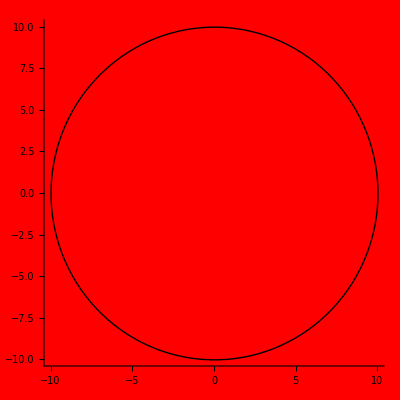

```mathematica
gr1=Graphics[Circle[{0,0},10],Axes->True,Background->RGBColor[1,0,0,0.1]]
```

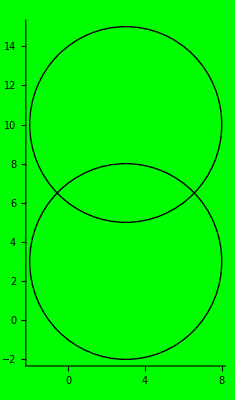

```mathematica
gr2=Graphics[{Circle[{3,3},5],Circle[{3,10},5]},Axes->True,Background->RGBColor[0,1,0,0.1]]
```

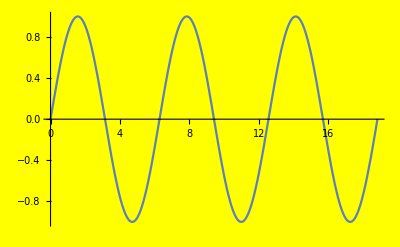

```mathematica
gr3=Plot[Sin[x],{x,0,6 Pi},Background->RGBColor[1,1,0,0.1]]
```

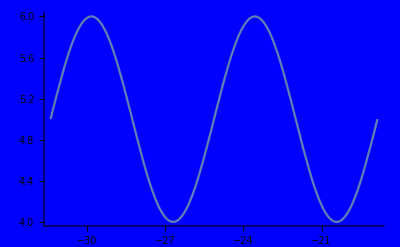

```mathematica
gr4=Plot[Sin[x]+5,{x,-10 Pi,-6Pi},Background->RGBColor[0,0,1,0.1], Axes->{True,True}]
```

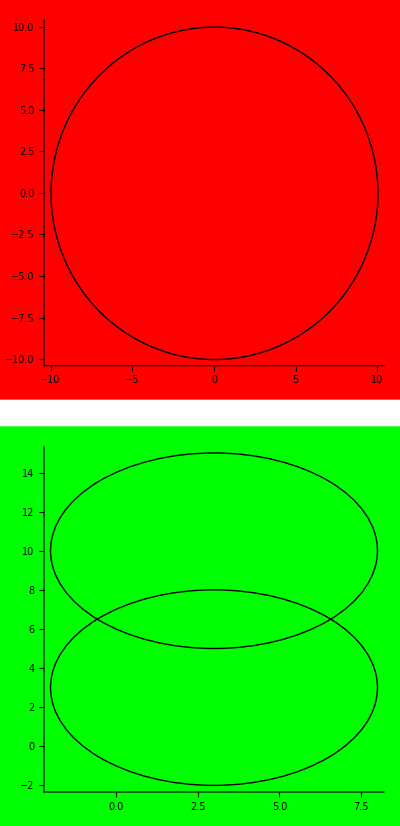

```mathematica
GraphicsColumn[{gr1, gr2}(*,Alignment-> Full*)]
```

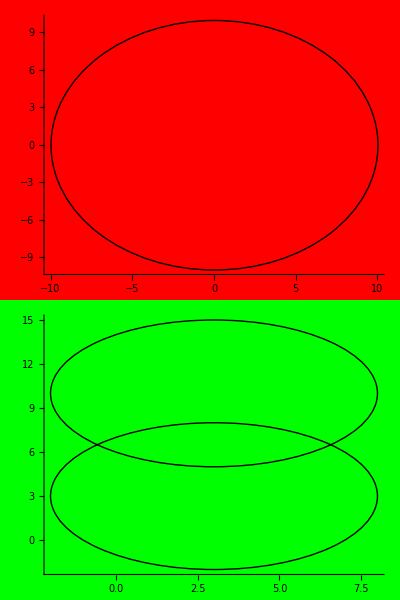

```mathematica
Column[{gr1, gr2}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\prog\_w\HokahokaW\HokahokaW\Tests\Graphics

```mathematica
Column[{Show[gr1,ImageSize->72*5], Show[gr2,ImageSize->72*5]}]
```

-Graphics-

```mathematica
Export["gcol.png", %]
```

gcol.png

```mathematica
Export["gcol.pdf", %%]
```

gcol.pdf

## Testing with Inset

```mathematica
HHGraphicsColumn[list:{__}, opts:OptionsPattern[]]:= 
Module[{optImageSize,optSpacings, 
tempPlotRange1,tempPlotWidth1,tempHeights,
tempAspectRatios,
tempPlotRange

},

optImageSize = OptionValue[ImageSize];
If[ optImageSize == Automatic,
optImageSize = HHAbsoluteOptionValue[list[[1]], ImageSize]
];

tempPlotRange1=HHAbsoluteOptionValue[list[[1]], PlotRange];
tempPlotWidth1 =(-Subtract@@tempPlotRange1[[1]]);
(*Print[{tempPlotRange1}];*)
optSpacings = OptionValue[Spacings];
optSpacings = 
If[ NumberQ[optSpacings],optSpacings,
If[Head[optSpacings]==Scaled, optSpacings[[1]]*(-Subtract@@tempPlotRange1[[2]]),0]
];
Print[optSpacings];

tempAspectRatios = HHAbsoluteOptionValue[#, AspectRatio]& /@  list;(*Print[tempAspectRatios];*)

tempHeights = tempPlotWidth1 * tempAspectRatios;
tempPlotRange ={
tempPlotRange1[[1]],
{tempPlotRange1[[2,1]]-optSpacings*(Length[list]-1)-Plus@@tempHeights[[2;;]],
 tempPlotRange1[[2,2]]}};

Graphics[
Flatten[{Inset[list[[1]],
tempPlotRange1[[All, 1]], 
{Left, Bottom},tempPlotWidth1
],
Table[
Inset[list[[li]], 
tempPlotRange1[[All, 1]]-{0,optSpacings*(li-1)+Plus@@tempHeights[[2 ;; li]]}, 
{Left,Bottom},tempPlotWidth1]
,{li, 2,Length[list]}]
}],PlotRange-> tempPlotRange, ImageSize->optImageSize, Axes->True, AxesOrigin->{-10,0}
]
];
```

```mathematica
Options[HHGraphicsColumn]= HHJoinOptionLists[
{Spacings-> Scaled[0.05]},
Options[Graphics]
]
```

{Spacings→Scaled[0.05],AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

### Function Tests

1.

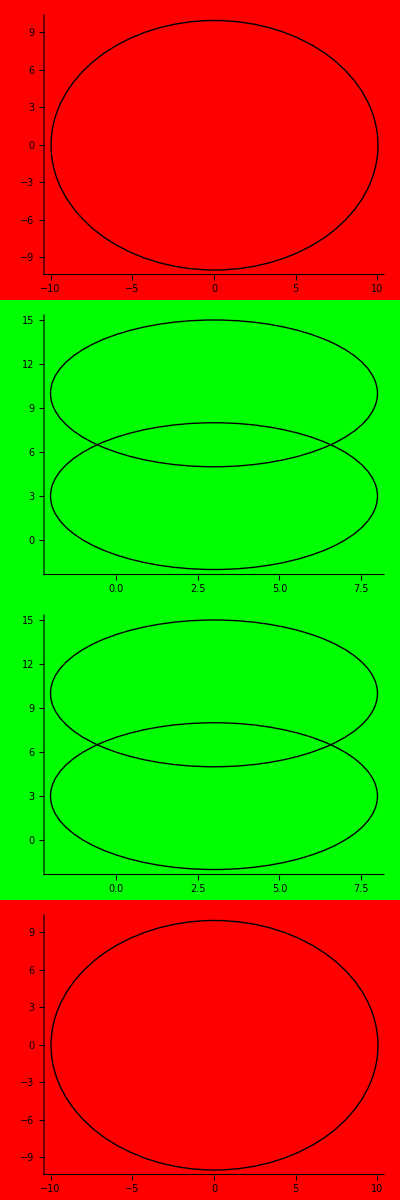

```mathematica
HHGraphicsColumn[{gr1, gr2,gr2, gr1}, Axes->True]
```

```mathematica
HHGraphicsColumn[{gr1, gr2,gr2, gr1},Spacings->0] //InputForm
```

0

Graphics[{Inset[Graphics[Circle[{0, 0}, 10], Axes -> True, Background -> RGBColor[1, 0, 0, 0.1]], 
   {-10., -10.}, {Left, Bottom}, 20.], Inset[Graphics[{Circle[{3, 3}, 5], Circle[{3, 10}, 5]}, 
    Axes -> True, Background -> RGBColor[0, 1, 0, 0.1]], {-10., -44.}, {Left, Bottom}, 20.], 
  Inset[Graphics[{Circle[{3, 3}, 5], Circle[{3, 10}, 5]}, Axes -> True, 
    Background -> RGBColor[0, 1, 0, 0.1]], {-10., -78.}, {Left, Bottom}, 20.], 
  Inset[Graphics[Circle[{0, 0}, 10], Axes -> True, Background -> RGBColor[1, 0, 0, 0.1]], {-10., -98.}, 
   {Left, Bottom}, 20.]}, PlotRange -> {{-10., 10.}, {-98., 10.}}, ImageSize -> Automatic]

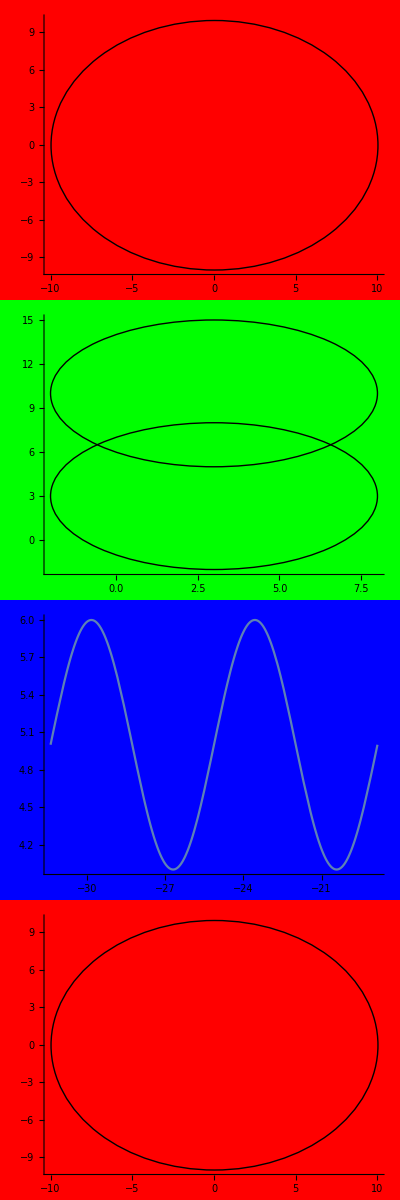

```mathematica
HHGraphicsColumn[{gr1, gr2,gr4, gr1}]
```

0

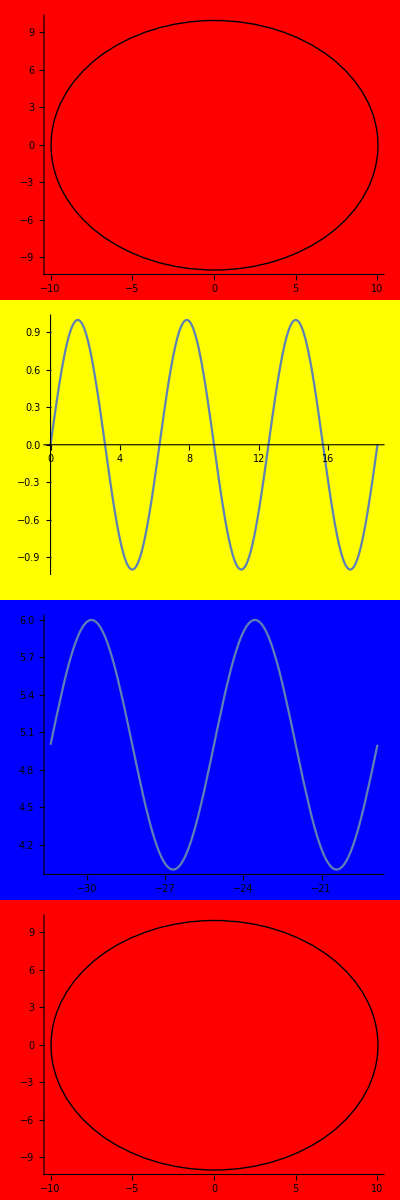

```mathematica
HHGraphicsColumn[{gr1, gr3,gr4, gr1},Spacings->0]
```

### Playing Around

```mathematica
HHOptionValue[gr1, PlotRange]
```

All

```mathematica
HHAbsoluteOptionValue[gr1, PlotRange]
```

{{-10.,10.},{-10.,10.}}

```mathematica
Range[10][[2;;2]]
```

{2}

## Inset Testing

```mathematica
Plot[Sin[x],{x,0,10},Epilog->Inset[Plot[Sin[x],{x,0,10}],{0.5,Center}]]
```

-Graphics-

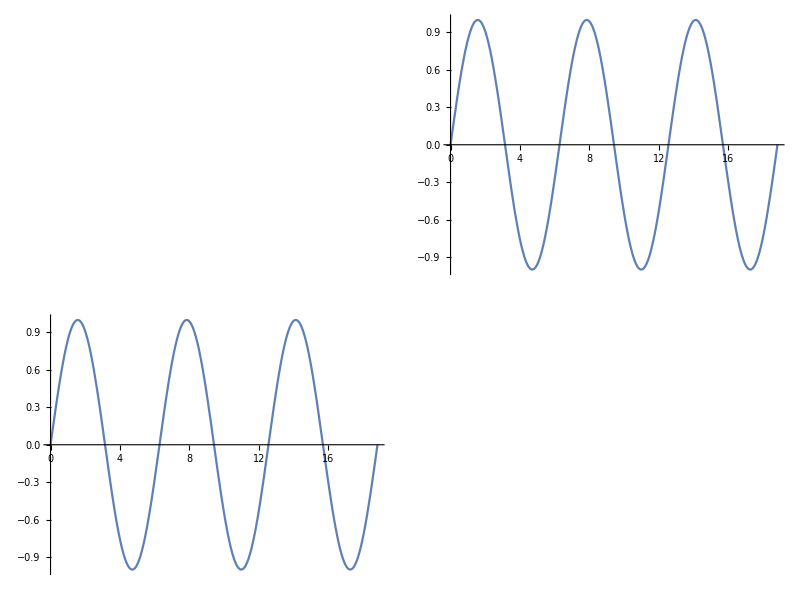

```mathematica
Graphics[{Inset[gr3, {0, 0}, {Left, Top}],Inset[gr3, {0.5, 0.5}, {Left, Top}]}, Axes->True]
```

```mathematica
HHAbsoluteOptionValue[gr2,ImageSize]
```

Automatic

```mathematica
Graphics[
Inset[gr1, ImageScaled[{0,0}],{Left, Bottom},1(*,ImageScaled[{1,1}]*)],
Axes->True, PlotRange-> {{-1,1},{-3,1}}
]
```

-Graphics-

```mathematica
Options[Graphics]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
HHAbsoluteOptionValue[#, PlotRangePadding]& /@ {gr1, gr2, gr3, gr4}
```

{Automatic,Automatic,{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}}}

```mathematica
HHAbsoluteOptionValue[#, ImageMargins]& /@ {gr1, gr2, gr3, gr4}
```

{0.,0.,0.,0.}

## FullGraphics/Translate Testing

```mathematica
FullGraphics[gr1] //InputForm
```

Graphics[{Circle[{0, 0}, 10], {{GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{-10., 0.}, {-10., 0.125}}]}, Text[-10, {-10., -0.25}, {0., 1.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{-7.5, 0.}, {-7.5, 0.125}}]}, 
   Text[-7.5, {-7.5, -0.25}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{-5., 0.}, {-5., 0.125}}]}, Text[-5, {-5., -0.25}, {0., 1.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{-2.5, 0.}, {-2.5, 0.125}}]}, 
   Text[-2.5, {-2.5, -0.25}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{2.5, 0.}, {2.5, 0.125}}]}, Text[2.5, {2.5, -0.25}, {0., 1.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{5., 0.}, {5., 0.125}}]}, 
   Text[5, {5., -0.25}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{7.5, 0.}, {7.5, 0.125}}]}, Text[7.5, {7.5, -0.25}, {0., 1.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{10., 0.}, {10., 0.125}}]}, 
   Text[10, {10., -0.25}, {0., 1.}], {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-9.5, 0.}, {-9.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-9., 0.}, {-9., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-8.5, 0.}, {-8.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-8., 0.}, {-8., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-7., 0.}, {-7., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-6.5, 0.}, {-6.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-6., 0.}, {-6., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-5.5, 0.}, {-5.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-4.5, 0.}, {-4.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-4., 0.}, {-4., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-3.5, 0.}, {-3.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-3., 0.}, {-3., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-2., 0.}, {-2., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-1.5, 0.}, {-1.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-1., 0.}, {-1., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{-0.5, 0.}, {-0.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.5, 0.}, {0.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{1., 0.}, {1., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{1.5, 0.}, {1.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{2., 0.}, {2., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{3., 0.}, {3., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{3.5, 0.}, {3.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{4., 0.}, {4., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{4.5, 0.}, {4.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{5.5, 0.}, {5.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{6., 0.}, {6., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{6.5, 0.}, {6.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{7., 0.}, {7., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{8., 0.}, {8., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{8.5, 0.}, {8.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{9., 0.}, {9., 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{9.5, 0.}, {9.5, 0.075}}]}, {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{-10., 0.}, {10., 0.}}]}, {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., -10.}, {0.125, -10.}}]}, Text[-10, {-0.25, -10.}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., -7.5}, {0.125, -7.5}}]}, 
   Text[-7.5, {-0.25, -7.5}, {1., 0.}], {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., -5.}, {0.125, -5.}}]}, Text[-5, {-0.25, -5.}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., -2.5}, {0.125, -2.5}}]}, 
   Text[-2.5, {-0.25, -2.5}, {1., 0.}], {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 2.5}, {0.125, 2.5}}]}, Text[2.5, {-0.25, 2.5}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., 5.}, {0.125, 5.}}]}, 
   Text[5, {-0.25, 5.}, {1., 0.}], {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 7.5}, {0.125, 7.5}}]}, Text[7.5, {-0.25, 7.5}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., 10.}, {0.125, 10.}}]}, 
   Text[10, {-0.25, 10.}, {1., 0.}], {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -9.5}, {0.075, -9.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -9.}, {0.075, -9.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -8.5}, {0.075, -8.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -8.}, {0.075, -8.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -7.}, {0.075, -7.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -6.5}, {0.075, -6.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -6.}, {0.075, -6.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -5.5}, {0.075, -5.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -4.5}, {0.075, -4.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -4.}, {0.075, -4.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -3.5}, {0.075, -3.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -3.}, {0.075, -3.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -2.}, {0.075, -2.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -1.5}, {0.075, -1.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -1.}, {0.075, -1.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., -0.5}, {0.075, -0.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.5}, {0.075, 0.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 1.}, {0.075, 1.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 1.5}, {0.075, 1.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 2.}, {0.075, 2.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 3.}, {0.075, 3.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 3.5}, {0.075, 3.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 4.}, {0.075, 4.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 4.5}, {0.075, 4.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 5.5}, {0.075, 5.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 6.}, {0.075, 6.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 6.5}, {0.075, 6.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 7.}, {0.075, 7.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 8.}, {0.075, 8.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 8.5}, {0.075, 8.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 9.}, {0.075, 9.}}]}, {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 9.5}, {0.075, 9.5}}]}, {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., -10.}, {0., 10.}}]}}}]

```mathematica
FullGraphics[gr3] //InputForm
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

Graphics[{{{{}, {}, {Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], 
      AbsoluteThickness[1.6]], Line[{{3.8468481472528077*^-7, 3.846848147252713*^-7}, 
      {0.005781496359763016, 0.005781464151389548}, {0.011562608034711307, 0.01156235039473104}, 
      {0.02312483138460789, 0.02312277040895298}, {0.04624927808440105, 0.04623279201301005}, 
      {0.09249817148398738, 0.09236632686747191}, {0.18499595828316004, 0.183942560776542}, 
      {0.36999153188150535, 0.3616075368935581}, {0.37625891940002865, 0.3674436726251089}, 
      {0.382526306918552, 0.37326537516268427}, {0.39506108195559864, 0.3848645665255114}, 
      {0.42013063202969186, 0.4078797282416327}, {0.4702697321778784, 0.45312675355728227}, 
      {0.5705479324742514, 0.5400932725884197}, {0.5768153199927748, 0.545357296338594}, 
      {0.5830827075112981, 0.5505998984444989}, {0.5956174825483447, 0.5610200148550174}, 
      {0.6206870326224379, 0.5815941844154343}, {0.6708261327706244, 0.6216333158173983}, 
      {0.7711043330669974, 0.6969276264714603}, {0.7769563914313835, 0.7011124225746124}, 
      {0.7828084497957697, 0.7052732080386412}, {0.794512566524542, 0.7135221779073093}, 
      {0.8179207999820868, 0.7297257760047864}, {0.864737266897176, 0.7609248181344146}, 
      {0.8705893252615622, 0.7647088168497773}, {0.8764413836259484, 0.7684666269727767}, 
      {0.8881455003547207, 0.7759031675757427}, {0.9115537338122653, 0.7904563838635271}, 
      {0.9583702007273547, 0.8182557582718716}, {0.9642222590917409, 0.8216058090350165}, 
      {0.970074317456127, 0.8249277226835604}, {0.9817784341848993, 0.8314866845488168}, 
      {1.005186667642444, 0.844262022330826}, {1.0520031345575331, 0.868418186400218}, 
      {1.0578551929219193, 0.8713049403445052}, {1.0637072512863055, 0.8741618551534198}, 
      {1.0754113680150779, 0.8797857770331563}, {1.0988196014726226, 0.8906713151143545}, 
      {1.1456360683877118, 0.910972643383592}, {1.1513733325971982, 0.9133240684466706}, 
      {1.1571105968066848, 0.9156454304339545}, {1.1685851252256576, 0.9201976605323836}, 
      {1.1915341820636032, 0.928938068377687}, {1.1972714462730896, 0.9310469050767217}, 
      {1.203008710482576, 0.9331250953331159}, {1.2144832389015487, 0.9371892639052373}, 
      {1.2374322957394943, 0.9449469017376344}, {1.2431695599489807, 0.9468087082993966}, 
      {1.248906824158467, 0.9486393496012645}, {1.2603813525774399, 0.9522068964227761}, 
      {1.2833304094153855, 0.9589654245854047}, {1.2890676736248718, 0.9605762795481013}, 
      {1.2948049378343582, 0.9621555160760097}, {1.306279466253331, 0.9652189269406336}, 
      {1.3292285230912766, 0.9709641101683963}, {1.334965787300763, 0.972320620641316}, 
      {1.3407030515102494, 0.9736451261014203}, {1.3521775799292222, 0.976197948647827}, 
      {1.3579148441387086, 0.9774261817051411}, {1.363652108348195, 0.9786222416944286}, 
      {1.3751266367671677, 0.9809176860506619}, {1.3808639009766541, 0.982016994860508}, 
      {1.3866011651861405, 0.9830839794906153}, {1.3980756936051133, 0.9851208367928207}, 
      {1.421024750443059, 0.9888051873434061}, {1.4267620146525455, 0.9896449790522676}, 
      {1.432499278862032, 0.990452195497821}, {1.4439738072810049, 0.9919687973904274}, 
      {1.4497110714904913, 0.992678132916845}, {1.4554483356999777, 0.9933547933403274}, 
      {1.4669228641189505, 0.9946100008626404}, {1.4726601283284368, 0.9951885066449218}, 
      {1.4783973925379232, 0.9957342546925294}, {1.4841346567474096, 0.9962472270415602}, 
      {1.489871920956896, 0.9967274068069599}, {1.4956091851663824, 0.9971747781830783}, 
      {1.5013464493758688, 0.9975893264441897}, {1.5070837135853552, 0.9979710379449782}, 
      {1.5128209777948416, 0.9983199001209855}, {1.519044517847903, 0.9986611739845765}, 
      {1.5252680579009645, 0.9989637673782378}, {1.5314915979540258, 0.999227668581823}, 
      {1.5377151380070873, 0.9994528673738251}, {1.5439386780601487, 0.9996393550317709}, 
      {1.55016221811321, 0.9997871243325599}, {1.5563857581662714, 0.9998961695527432}, 
      {1.562609298219333, 0.999966486468746}, {1.5688328382723944, 0.9999980723570303}, 
      {1.5750563783254559, 0.9999909259942015}, {1.5812799183785171, 0.9999450476570546}, 
      {1.5875034584315786, 0.9998604391225645}, {1.59372699848464, 0.9997371036678164}, 
      {1.5999505385377013, 0.9995750460698795}, {1.6061740785907628, 0.9993742726056212}, 
      {1.6123976186438242, 0.9991347910514649}, {1.6186211586968857, 0.9988566106830882}, 
      {1.6248446987499472, 0.9985397422750635}, {1.6310682388030084, 0.9981841981004416}, 
      {1.63729177885607, 0.997789991930275}, {1.6435153189091314, 0.9973571390330855}, 
      {1.6497388589621926, 0.9968856561742727}, {1.6621859390683156, 0.9958268751138087}, 
      {1.668409479121377, 0.9952396179212104}, {1.6746330191744385, 0.9946138127835064}, 
      {1.6870800992805615, 0.9932466571204472}, {1.693303639333623, 0.9925053595482107}, 
      {1.6995271793866844, 0.9917256199350545}, {1.7119742594928071, 0.9900509368782774}, 
      {1.7181977995458686, 0.9891560582990263}, {1.7244213395989298, 0.9882228674050825}, 
      {1.7368684197050528, 0.9862416947342568}, {1.7430919597581143, 0.9851937896928002}, 
      {1.7493154998111757, 0.9841077258045294}, {1.7617625799172987, 0.9818212912270182}, 
      {1.7679861199703601, 0.9806210090967066}, {1.7742096600234216, 0.9793827452340086}, 
      {1.7866567401295443, 0.9767924656240736}, {1.81155090034179, 0.9711583342243256}, 
      {1.8177744403948515, 0.969655623279964}, {1.823997980447913, 0.9681153553181117}, 
      {1.8364450605540357, 0.9649223884269365}, {1.8613392207662813, 0.9580884925677529}, 
      {1.9111275411907727, 0.9426441580931141}, {1.9169357520896968, 0.9406894919468624}, 
      {1.9227439629886212, 0.938703091434582}, {1.9343603847864697, 0.9346353564268658}, 
      {1.9575932283821669, 0.9261220939787911}, {2.004058915573561, 0.9076008363535164}, 
      {2.0098671264724857, 0.9051470556640222}, {2.01567533737141, 0.9026627396403718}, 
      {2.027291759169258, 0.8976028378536706}, {2.0505246027649555, 0.8871203665310926}, 
      {2.0969902899563495, 0.8647248951211541}, {2.1027985008552736, 0.861793176081398}, 
      {2.108606711754198, 0.858832384260108}, {2.1202231335520465, 0.8528239827821747}, 
      {2.1434559771477435, 0.8404627665929759}, {2.189921664339138, 0.8143863549156388}, 
      {2.2828530387219264, 0.7570196386853174}, {2.2891475254644256, 0.7528919010638034}, 
      {2.295442012206925, 0.7487343335395165}, {2.3080309856919237, 0.7403303688564651}, 
      {2.333208932661921, 0.7231718069194039}, {2.383564826601915, 0.6874906042506518}, 
      {2.484276614481904, 0.610994337927606}, {2.6857001902418816, 0.44026380373010093}, 
      {2.691879882829481, 0.43470688143573194}, {2.698059575417081, 0.42913335834677335}, 
      {2.7104189605922797, 0.417937361788395}, {2.735137730942678, 0.39535556576229824}, 
      {2.784575271643474, 0.34948124773468864}, {2.883450353045067, 0.2552848471903414}, 
      {3.081200515848252, 0.060355433964355304}, {3.450119775589845, -0.30365563489449215}, 
      {3.456370414866883, -0.30960515980541903}, {3.46262105414392, -0.3155425883300051}, 
      {3.475122332697995, -0.3273802287918519}, {3.500124889806145, -0.35090017884779023}, 
      {3.550130004022444, -0.39726747570690585}, {3.6501402324550423, -0.4869091398489468}, 
      {3.6563908717320794, -0.492359229728036}, {3.662641511009117, -0.4977900829527209}, 
      {3.675142789563192, -0.5085932314570971}, {3.7001453466713414, -0.5299594038280652}, 
      {3.7501504608876406, -0.5716847743615057}, {3.8501606893202394, -0.6507471559833308}, 
      {3.85599599944314, -0.6551667705117512}, {3.86183130956604, -0.6595640761218268}, 
      {3.87350192981184, -0.6682911624255046}, {3.896843170303441, -0.6854710913453013}, 
      {3.9435256512866435, -0.7187014823324376}, {3.9493609614095435, -0.7227466237490302}, 
      {3.955196271532444, -0.7267671551027527}, {3.9668668917782446, -0.7347338408558453}, 
      {3.9902081322698457, -0.7503659246316192}, {4.036890613253048, -0.7803954259100183}, 
      {4.042725923375948, -0.7840308582590282}, {4.048561233498848, -0.7876395937711659}, 
      {4.060231853744649, -0.7947764836774884}, {4.08357309423625, -0.808724556139615}, 
      {4.1302555752194525, -0.8352915901599574}, {4.223620537185856, -0.8829117918457624}, 
      {4.229341053153856, -0.8855833356084009}, {4.235061569121857, -0.8882258993527158}, 
      {4.246502601057858, -0.8934237418342692}, {4.26938466492986, -0.9034679255261711}, 
      {4.315148792673864, -0.9221322065076192}, {4.320869308641864, -0.9243302304949753}, 
      {4.326589824609865, -0.9264980065023394}, {4.338030856545866, -0.9307425318141918}, 
      {4.360912920417868, -0.9388655519744901}, {4.406677048161872, -0.9536329224706064}, 
      {4.412397564129872, -0.9553390257605613}, {4.418118080097873, -0.9570138663320812}, 
      {4.429559112033874, -0.9602695411132937}, {4.452441175905876, -0.9664033952714969}, 
      {4.458161691873876, -0.9678579197068659}, {4.463882207841877, -0.9692807717528391}, 
      {4.475323239777878, -0.9720312734677176}, {4.49820530364988, -0.9771502291362688}, 
      {4.50392581961788, -0.9783501289575943}, {4.509646335585881, -0.9795180130402265}, 
      {4.521087367521882, -0.9817575821659967}, {4.526807883489882, -0.9828291939209963}, 
      {4.532528399457883, -0.9838686433634233}, {4.543969431393884, -0.9858509203034959}, 
      {4.549689947361884, -0.9867936829326871}, {4.555410463329885, -0.9877041535145202}, 
      {4.566851495265886, -0.9894281004160825}, {4.572572011233886, -0.990241520321005}, 
      {4.578292527201887, -0.9910225353508018}, {4.589733559137888, -0.992487249613867}, 
      {4.595940350949464, -0.9932275166091267}, {4.602147142761039, -0.9939295203675749}, 
      {4.608353934572614, -0.9945932338451201}, {4.614560726384189, -0.9952186314727708}, 
      {4.620767518195764, -0.9958056891576205}, {4.62697431000734, -0.9963543842837764}, 
      {4.6393878936304915, -0.997336603786672}, {4.645594685442067, -0.9977700903242492}, 
      {4.651801477253643, -0.9981651386262652}, {4.658008269065219, -0.9985217334738234}, 
      {4.664215060876794, -0.9988398611294138}, {4.670421852688369, -0.9991195093374418}, 
      {4.676628644499945, -0.9993606673247002}, {4.682835436311521, -0.999563325800785}, 
      {4.689042228123096, -0.9997274769584522}, {4.695249019934671, -0.9998531144739197}, 
      {4.701455811746247, -0.9999402335071101}, {4.707662603557823, -0.9999888307018375}, 
      {4.713869395369398, -0.9999989041859366}, {4.7200761871809735, -0.9999704535713353}, 
      {4.72628297899255, -0.9999034799540689}, {4.732489770804126, -0.9997979859142385}, 
      {4.738696562615701, -0.9996539755159115}, {4.744903354427276, -0.9994714543069646}, 
      {4.751110146238852, -0.9992504293188705}, {4.757316938050428, -0.9989909090664273}, 
      {4.763523729862003, -0.9986929035474296}, {4.769730521673578, -0.998356424242284}, 
      {4.775937313485153, -0.9979814841135666}, {4.782144105296728, -0.9975680976055239}, 
      {4.788350897108304, -0.9971162806435159}, {4.79455768891988, -0.9966260506334029}, 
      {4.800764480731456, -0.996097426460875}, {4.806971272543031, -0.9955304284907242}, 
      {4.813178064354606, -0.9949250785660603}, {4.819384856166181, -0.9942814000074689}, 
      {4.825591647977757, -0.9935994176121137}, {4.838005231600908, -0.9921206478768655}, 
      {4.844212023412483, -0.9913239175053064}, {4.850418815224059, -0.9904889972314558}, 
      {4.86283239884721, -0.9887047171052205}, {4.887659566093513, -0.9846793916825087}, 
      {4.893866357905088, -0.9835781249268344}, {4.900073149716664, -0.9824389666688735}, 
      {4.912486733339815, -0.9800471526445128}, {4.937313900586117, -0.9748108551022111}, 
      {4.943520692397692, -0.9734077666360691}, {4.9497274842092684, -0.9719671784719565}, 
      {4.96214106783242, -0.9689737264820115}, {4.986968235078721, -0.9625393645365065}, 
      {4.99275969773616, -0.9609529224394434}, {4.998551160393598, -0.9593342490723367}, 
      {5.010134085708474, -0.9560004267745809}, {5.033299936338228, -0.9489484679838083}, 
      {5.0796316375977355, -0.9333208978336991}, {5.0854231002551735, -0.9312258712767412}, 
      {5.091214562912612, -0.9290996105231556}, {5.102797488227489, -0.9247536727385233}, 
      {5.125963338857242, -0.9156901946424798}, {5.172295040116749, -0.8960941981758537}, 
      {5.178086502774187, -0.8935085632492759}, {5.183877965431626, -0.8908929592002606}, 
      {5.195460890746503, -0.885572195656506}, {5.218626741376256, -0.8745749661956119}, 
      {5.264958442635763, -0.8511786841934744}, {5.357621845154776, -0.7989597473420631}, 
      {5.3638995836557894, -0.7951686940321228}, {5.3701773221568025, -0.791346303226322}, 
      {5.38273279915883, -0.7836081129159269}, {5.407843753162883, -0.7677623925128859}, 
      {5.45806566117099, -0.7346289636213397}, {5.558509477187204, -0.6628927667610891}, 
      {5.564787215688218, -0.6581795024652893}, {5.571064954189231, -0.6534402994000333}, 
      {5.5836204311912585, -0.6438848250615632}, {5.608731385195312, -0.6244708966735887}, 
      {5.658953293203419, -0.5844742921141424}, {5.759397109219633, -0.5001640356060488}, 
      {5.765560053565746, -0.49481788826262274}, {5.77172299791186, -0.48945294686353735}, 
      {5.784048886604088, -0.47866749768420896}, {5.808700663988542, -0.4568800834071375}, 
      {5.858004218757451, -0.41248575354855727}, {5.956611328295269, -0.3207999719449769}, 
      {6.153825547370905, -0.12899927831752625}, {6.5216729196574, 0.2362333157037078}, 
      {6.527906810692951, 0.24228613554913578}, {6.534140701728503, 0.2483295398472479}, 
      {6.546608483799606, 0.260387162759045}, {6.571544047941812, 0.28437911405896626}, 
      {6.621415176226224, 0.33181777132940776}, {6.721157432795048, 0.42410386781156284}, 
      {6.727391323830599, 0.4297410868548895}, {6.733625214866151, 0.4353616056131262}, 
      {6.746092996937254, 0.446551669249785}, {6.77102856107946, 0.46872182712424854}, 
      {6.820899689363872, 0.5121742561819896}, {6.9206419459326955, 0.5951534927608837}, 
      {6.9264605078141095, 0.5998192581641794}, {6.932279069695524, 0.6044647163464825}, 
      {6.943916193458353, 0.6136940826424654}, {6.967190440984011, 0.6319022552155189}, 
      {7.013738936035325, 0.6672820828349127}, {7.106835926137954, 0.7336314818764441}, 
      {7.112654488019368, 0.7375730301794905}, {7.118473049900783, 0.741489607529507}, 
      {7.130110173663612, 0.7492473198285572}, {7.153384421189269, 0.7644573158725865}, 
      {7.199932916240584, 0.793627051570115}, {7.293029906343214, 0.8467491827921635}, 
      {7.299334744068203, 0.850086456278428}, {7.3056395817931925, 0.8533899381079817}, 
      {7.3182492572431705, 0.8598950028806163}, {7.343468608143128, 0.8724939452675943}, 
      {7.393907309943044, 0.8960194990375716}, {7.400212147668034, 0.8988011123798837}, 
      {7.406516985393023, 0.9015469976166395}, {7.419126660843002, 0.9069311485929892}, 
      {7.444346011742959, 0.9172660063072194}, {7.494784713542874, 0.9361794260896075}, 
      {7.501089551267864, 0.9383770968899147}, {7.507394388992853, 0.9405374664057583}, 
      {7.520004064442832, 0.9447459595641543}, {7.545223415342789, 0.9527116516602608}, 
      {7.551528253067778, 0.9546085910994466}, {7.5578330907927675, 0.9564675840385255}, 
      {7.570442766242746, 0.960071436341528}, {7.5956621171427035, 0.9668206329177365}, 
      {7.601966954867693, 0.9684120160860814}, {7.608271792592682, 0.9699649040564833}, 
      {7.620881468042661, 0.9729549490216807}, {7.62718630576765, 0.9743919871596559}, 
      {7.633491143492639, 0.9757902923907728}, {7.646100818942618, 0.9784704833390374}, 
      {7.652405656667607, 0.9797522625163246}, {7.658710494392597, 0.9809950957112678}, 
      {7.671320169842575, 0.9833637280895315}, {7.696539520742533, 0.9876315712578209}, 
      {7.702729564312623, 0.9885831959954859}, {7.708919607882713, 0.9894969416682639}, 
      {7.721299695022892, 0.9912106572256859}, {7.727489738592981, 0.9920105614467188}, 
      {7.733679782163071, 0.9927724552781578}, {7.7460598693032505, 0.9941820964573257}, 
      {7.75224991287334, 0.9948297897925144}, {7.758439956443429, 0.9954393647150978}, 
      {7.764630000013518, 0.9960107978682883}, {7.770820043583608, 0.9965440673567576}, 
      {7.777010087153698, 0.9970391527474762}, {7.783200130723788, 0.9974960350704966}, 
      {7.789390174293878, 0.9979146968196789}, {7.795580217863967, 0.9982951219533636}, 
      {7.801770261434056, 0.9986372958949842}, {7.807960305004146, 0.9989412055336273}, 
      {7.814150348574236, 0.9992068392245339}, {7.820340392144326, 0.9994341867895462}, 
      {7.826530435714416, 0.9996232395174973}, {7.832720479284505, 0.9997739901645452}, 
      {7.838910522854594, 0.99988643295445}, {7.845100566424684, 0.9999605635787959}, 
      {7.8512906099947735, 0.9999963791971553}, {7.857480653564863, 0.9999938784371987}, 
      {7.863670697134953, 0.9999530613947463}, {7.869860740705042, 0.999873929633765}, 
      {7.876050784275131, 0.9997564861863084}, {7.882240827845221, 0.9996007355524004}, 
      {7.888430871415311, 0.9994066836998626}, {7.894620914985401, 0.9991743380640863}, 
      {7.900810958555491, 0.9989037075477468}, {7.907001002125581, 0.9985948025204632}, 
      {7.913191045695671, 0.9982476348184001}, {7.91938108926576, 0.9978622177438147}, 
      {7.925571132835849, 0.9974385660645468}, {7.931761176405939, 0.9969766960134533}, 
      {7.944141263546118, 0.9959383730485128}, {7.950331307116208, 0.9953619599195856}, 
      {7.956521350686297, 0.9947474079871476}, {7.968901437826476, 0.9934039833621411}, 
      {7.975091481396566, 0.9926751621449252}, {7.981281524966656, 0.9919083050729312}, 
      {7.993661612106835, 0.9902606023540528}, {7.999851655676924, 0.9893798198413979}, 
      {8.006041699247014, 0.9884611277400042}, {8.018421786387194, 0.9865101570265421}, 
      {8.024611829957284, 0.9854779531688763}, {8.030801873527373, 0.9844079892284129}, 
      {8.043181960667551, 0.9821549465335236}, {8.04937200423764, 0.9809719541078468}, 
      {8.05556204780773, 0.9797513742535617}, {8.06794213494791, 0.9771976407710707}, 
      {8.092702309228269, 0.9716412787406759}, {8.098477023644222, 0.9702595978807996}, 
      {8.104251738060174, 0.9688455615471542}, {8.115801166892078, 0.9659206121527503}, 
      {8.138900024555888, 0.9596845945577898}, {8.14467473897184, 0.9580454504447878}, 
      {8.150449453387793, 0.9563743581660481}, {8.161998882219699, 0.9529365530801008}, 
      {8.185097739883508, 0.945680088025887}, {8.190872454299459, 0.9437869783463612}, 
      {8.196647168715412, 0.9418623959817014}, {8.208196597547317, 0.9379190709623617}, 
      {8.231295455211129, 0.9296576426521387}, {8.277493170538747, 0.9116514479212036}, 
      {8.2832678849547, 0.9092630592455481}, {8.289042599370653, 0.9068443491619651}, 
      {8.300592028202558, 0.901916288408626}, {8.323690885866368, 0.8916999263400164}, 
      {8.369888601193988, 0.86984565144995}, {8.462284031849228, 0.820619337343879}, 
      {8.468545022108756, 0.8170252759789536}, {8.474806012368283, 0.813399187328626}, 
      {8.487327992887337, 0.8060514979904841}, {8.512371953925449, 0.7909781295732068}, 
      {8.562459876001668, 0.7593529307585913}, {8.662635720154107, 0.6904726362677394}, 
      {8.668896710413634, 0.685930192032572}, {8.67515770067316, 0.681360859422378}, 
      {8.687679681192217, 0.672142246592903}, {8.712723642230326, 0.6533903113449088}, 
      {8.762811564306547, 0.6146691035283012}, {8.862987408458988, 0.5327024001949159}, 
      {8.868833069564378, 0.5277461283023609}, {8.874678730669768, 0.5227718224504166}, 
      {8.88637005288055, 0.5127697893998834}, {8.90975269730211, 0.4925568354906324}, 
      {8.956517986145233, 0.4513342491170544}, {9.050048563831478, 0.36602071746698633}, 
      {9.23710971920397, 0.18656858697156647}, {9.603885204035366, -0.17815116911595913}, 
      {9.610102346829432, -0.18426537466206605}, {9.616319489623496, -0.19037245784655005}, 
      {9.628753775211628, -0.20256431319308654}, {9.653622346387891, -0.22685218867112536}, 
      {9.703359488740416, -0.2749921407413104}, {9.802833773445466, -0.3691142715234414}, 
      {9.809050916239531, -0.3748852138170158}, {9.815268059033595, -0.3806416657698822}, 
      {9.827702344621727, -0.39211020921162776}, {9.85257091579799, -0.4148636604725539}, 
      {9.902308058150515, -0.45958697816374755}, {10.001782342855565, -0.5455157591344861}, 
      {10.007584156495493, -0.5503690538543501}, {10.01338597013542, -0.5552038226306105}, 
      {10.024989597415278, -0.5648171320098233}, {10.048196851974993, -0.5838143212108748}, 
      {10.094611361094419, -0.6208553939845274}, {10.187440379333275, -0.6908488179824648}, 
      {10.193242192973203, -0.6950318740277314}, {10.199044006613132, -0.6991915346418602}, 
      {10.21064763389299, -0.7074401102964667}, {10.233854888452703, -0.723650408975727}, 
      {10.28026939757213, -0.7548933149296787}, {10.373098415810986, -0.8124373950784531}, 
      {10.37938650529449, -0.8160875697959559}, {10.385674594777992, -0.8197054764606747}, 
      {10.398250773745, -0.8268439147060588}, {10.423403131679013, -0.8407273664590242}, 
      {10.473707847547042, -0.8668902716767684}, {10.479995937030544, -0.8700077189693092}, 
      {10.48628402651405, -0.8730907662096541}, {10.498860205481055, -0.879153174284748}, 
      {10.52401256341507, -0.8908599177746925}, {10.574317279283097, -0.9125756608090112}, 
      {10.580605368766602, -0.9151288516804115}, {10.586893458250104, -0.9176458584127763}, 
      {10.599469637217112, -0.9225709228058847}, {10.624621995151125, -0.9319825592801961}, 
      {10.630910084634628, -0.9342435710240258}, {10.637198174118133, -0.9364676428339832}, 
      {10.649774353085139, -0.9408046163577024}, {10.674926711019154, -0.9490315131366599}, 
      {10.681214800502657, -0.9509946253234844}, {10.68750288998616, -0.9529201352407698}, 
      {10.700079068953167, -0.9566580452183457}, {10.72523142688718, -0.963679387999403}, 
      {10.731519516370685, -0.9653396338948533}, {10.737807605854188, -0.9669617103199991}, 
      {10.750383784821196, -0.9700910997239212}, {10.77553614275521, -0.975889124293324}, 
      {10.781709438083812, -0.977217946149371}, {10.787882733412417, -0.9785095267628697}, 
      {10.800229324069623, -0.9809807687976115}, {10.806402619398227, -0.98216033604117}, 
      {10.81257591472683, -0.9833024736903985}, {10.824922505384038, -0.9854742875289774}, 
      {10.831095800712642, -0.9865038809516876}, {10.837269096041245, -0.9874958792499422}, 
      {10.849615686698453, -0.989366940689201}, {10.855788982027057, -0.9902459325250748}, 
      {10.86196227735566, -0.99108718662895}, {10.874308868012868, -0.9926563548411526}, 
      {10.880482163341473, -0.9933842091493358}, {10.886655458670075, -0.9940742061275112}, 
      {10.892828753998678, -0.9947263194802707}, {10.899002049327283, -0.9953405243559305}, 
      {10.905175344655888, -0.9959167973474778}, {10.91134863998449, -0.9964551164934634}, 
      {10.923695230641698, -0.9974178126357369}, {10.929868525970303, -0.9978421529442003}, 
      {10.936041821298906, -0.998228466032851}, {10.942215116627509, -0.9985767371795082}, 
      {10.948388411956113, -0.9988869531117488}, {10.954561707284718, -0.9991591020074129}, 
      {10.96073500261332, -0.9993931734950543}, {10.966908297941924, -0.9995891586543366}, 
      {10.973081593270528, -0.9997470500163724}, {10.979254888599133, -0.9998668415640081}, 
      {10.985428183927736, -0.999948528732053}, {10.991601479256339, -0.9999921084074538}, 
      {10.997774774584943, -0.9999975789294129}, {11.003948069913548, -0.9999649400894517}, 
      {11.010121365242151, -0.9998941931314185}, {11.016294660570754, -0.9997853407514413}, 
      {11.022467955899359, -0.9996383870978249}, {11.028641251227963, -0.999453337770893}, 
      {11.034814546556566, -0.9992301998227741}, {11.040987841885169, -0.9989689817571338}, 
      {11.047161137213774, -0.9986696935288499}, {11.053334432542378, -0.9983323465436337}, 
      {11.059507727870981, -0.9979569536575944}, {11.065681023199584, -0.9975435291767502}, 
      {11.071854318528189, -0.997092088856482}, {11.078027613856793, -0.9966026499009344}, 
      {11.084200909185396, -0.996075230962359}, {11.090374204514, -0.9955098521404032}, 
      {11.096547499842604, -0.9949065349813455}, {11.102720795171209, -0.9942653024772736}, 
      {11.108894090499811, -0.9935861790652084}, {11.121240681157019, -0.992114364484203}, 
      {11.127413976485624, -0.9913217294053132}, {11.133587271814227, -0.9904913155963931}, 
      {11.145933862471434, -0.9887172798134507}, {11.170627043785847, -0.9847173522470988}, 
      {11.176385009960313, -0.9836982261934424}, {11.18214297613478, -0.9826464865272789}, 
      {11.193658908483712, -0.9804453069154068}, {11.216690773181579, -0.975653190898181}, 
      {11.222448739356047, -0.9743741926906572}, {11.228206705530512, -0.9730628900004065}, 
      {11.239722637879446, -0.9703435461414586}, {11.262754502577312, -0.9645191891109507}, 
      {11.26851246875178, -0.9629830321340238}, {11.274270434926246, -0.961414948337851}, 
      {11.285786367275179, -0.9581832092980671}, {11.308818231973046, -0.9513389675811167}, 
      {11.354881961368779, -0.9361404880432}, {11.360639927543247, -0.934100329008121}, 
      {11.366397893717712, -0.932029200733329}, {11.377913826066646, -0.9277943121545177}, 
      {11.400945690764512, -0.9189559939499378}, {11.447009420160244, -0.8998219420680568}, 
      {11.45276738633471, -0.8972950845169033}, {11.458525352509177, -0.8947384779701614}, 
      {11.470041284858109, -0.8895363579211875}, {11.493073149555975, -0.8787789251355327}, 
      {11.539136878951709, -0.8558715857444221}, {11.54538112096975, -0.8526254718656268}, 
      {11.551625362987792, -0.8493461137516122}, {11.564113847023876, -0.8426881775635016}, 
      {11.589090815096043, -0.8289790865909877}, {11.639044751240375, -0.8000183866946593}, 
      {11.738952623529041, -0.7361863778366209}, {11.745196865547083, -0.7319460822299381}, 
      {11.751441107565125, -0.7276772477295343}, {11.763929591601208, -0.7190546289286178}, 
      {11.788906559673373, -0.7014743218769192}, {11.838860495817705, -0.6650121738617065}, 
      {11.938768368106372, -0.5872056152513524}, {11.944597280970275, -0.5824775240288809}, 
      {11.95042619383418, -0.5777296424749255}, {11.962084019561988, -0.5681751542980302}, 
      {11.985399671017607, -0.5488358361851204}, {12.032030973928844, -0.5092728416837538}, 
      {12.125293579751315, -0.42691366668478975}, {12.311818791396256, -0.25181169884680005}, 
      {12.677522388772555, 0.11092304097063432}, {12.683722783325134, 0.1170830011923399}, 
      {12.689923177877715, 0.12323846018506103}, {12.702323966982874, 0.13553492808488224}, 
      {12.727125545193193, 0.16006344946050044}, {12.77672870161383, 0.20881010687879906}, 
      {12.875935014455106, 0.304643771102858}, {12.882135409007685, 0.31054354453162875}, 
      {12.888335803560265, 0.3164313791854305}, {12.900736592665424, 0.32817032721002276}, 
      {12.925538170875743, 0.3514950300966872}, {12.975141327296381, 0.397481622327319}, 
      {13.074347640137656, 0.48641070953222143}, {13.080132705536098, 0.4914571288870259}, 
      {13.085917770934541, 0.4964871007009816}, {13.097487901731427, 0.5064970289124022}, 
      {13.120628163325197, 0.5263121455662154}, {13.166908686512738, 0.5650864817472283}, 
      {13.259469732887819, 0.638924304391508}, {13.26525479828626, 0.6433638631688421}, 
      {13.271039863684704, 0.6477818905596147}, {13.28260999448159, 0.6565527604764898}, 
      {13.30575025607536, 0.6738296668218261}, {13.3520307792629, 0.7072920199566012}, 
      {13.44459182563798, 0.7696043028846435}, {13.450863166879998, 0.7735935263400635}, 
      {13.457134508122014, 0.7775523246776621}, {13.469677190606049, 0.7853780244104366}, 
      {13.49476255557412, 0.8006575526754123}, {13.544933285510261, 0.8296958883236634}, 
      {13.551204626752279, 0.8331803105216814}, {13.557475967994296, 0.8366319640779645}, 
      {13.570018650478332, 0.8434364235509365}, {13.595104015446402, 0.8566462327030046}, 
      {13.645274745382544, 0.8814407632720084}, {13.651546086624561, 0.8843853310519143}, 
      {13.65781742786658, 0.8872951163175157}, {13.670360110350614, 0.8930098829156178}, 
      {13.695445475318685, 0.9040170827546687}, {13.701716816560703, 0.9066802632487436}, 
      {13.70798815780272, 0.9093077843779255}, {13.720530840286756, 0.9144554365908059}, 
      {13.745616205254825, 0.9243183761677756}, {13.751887546496842, 0.9266934672846903}, 
      {13.758158887738858, 0.9290321119255603}, {13.770701570222894, 0.933599695304454}, 
      {13.795786935190964, 0.9422935538000384}, {13.845957665127106, 0.9578973797831336}, 
      {13.851813677214986, 0.9595622699900354}, {13.857669689302867, 0.9611942541395253}, 
      {13.869381713478628, 0.9643592815355387}, {13.89280576183015, 0.9702920770049214}, 
      {13.89866177391803, 0.9716922151544736}, {13.904517786005911, 0.9730590312770783}, 
      {13.916229810181672, 0.9756925110980617}, {13.939653858533193, 0.9805576208076399}, 
      {13.945509870621073, 0.9816899345167954}, {13.951365882708952, 0.9827885833494168}, 
      {13.963077906884713, 0.9848847368379239}, {13.968933918972594, 0.9858821696108798}, 
      {13.974789931060474, 0.986845793743908}, {13.986501955236236, 0.9886714850693064}, 
      {13.992357967324116, 0.9895334896536464}, {13.998213979411997, 0.9903615603841452}, 
      {14.009926003587758, 0.9919157878608913}, {14.015782015675638, 0.9926418913083582}, 
      {14.021638027763519, 0.9933339543062512}, {14.03335005193928, 0.9946158651904153}, 
      {14.03920606402716, 0.9952056691163992}, {14.045062076115041, 0.9957613446737418}, 
      {14.050918088202922, 0.9962828728067838}, {14.056774100290802, 0.996770235630876}, 
      {14.062630112378683, 0.9972234164329923}, {14.068486124466563, 0.9976423996723034}, 
      {14.074342136554442, 0.9980271709807095}, {14.080198148642323, 0.9983777171633329}, 
      {14.086054160730203, 0.9986940261989706}, {14.091910172818082, 0.9989760872405066}, 
      {14.097766184905963, 0.9992238906152838}, {14.103622196993843, 0.9994374278254357}, 
      {14.109478209081724, 0.9996166915481778}, {14.115334221169604, 0.9997616756360587}, 
      {14.121190233257485, 0.9998723751171711}, {14.127046245345365, 0.9999487861953221}, 
      {14.132902257433246, 0.9999909062501634}, {14.138758269521126, 0.9999987338372813}, 
      {14.144614281609007, 0.9999722686882461}, {14.150470293696888, 0.9999115117106211}, 
      {14.156326305784768, 0.9998164649879322}, {14.162182317872649, 0.9996871317795956}, 
      {14.16803832996053, 0.9995235165208065}, {14.17389434204841, 0.9993256248223871}, 
      {14.17975035413629, 0.9990934634705934}, {14.185606366224171, 0.9988270404268837}, 
      {14.191462378312051, 0.9985263648276449}, {14.197318390399932, 0.9981914469838786}, 
      {14.203174402487813, 0.997822298380849}, {14.209030414575693, 0.9974189316776876}, 
      {14.220742438751452, 0.9965096004741906}, {14.226483656684433, 0.9960139131300011}, 
      {14.232224874617415, 0.99548539568037}, {14.243707310483376, 0.9943299412292349}, 
      {14.249448528416357, 0.9937030423132346}, {14.255189746349338, 0.9930433894615445}, 
      {14.266672182215299, 0.991625910002568}, {14.27241340014828, 0.9908681301175206}, 
      {14.27815461808126, 0.9900776897397215}, {14.28963705394722, 0.9883989327979273}, 
      {14.312601925679143, 0.9846507114009697}, {14.318343143612124, 0.9836324372620538}, 
      {14.324084361545104, 0.9825817411296244}, {14.335566797411065, 0.9803832224818123}, 
      {14.358531669142987, 0.9755987165526131}, {14.364272887075968, 0.9743220958736175}, 
      {14.370014105008948, 0.973013360083859}, {14.38149654087491, 0.9702997167807348}, 
      {14.404461412606834, 0.964489017658122}, {14.410202630539814, 0.9629567430497398}, 
      {14.415943848472796, 0.9613927279495897}, {14.427426284338758, 0.9581696835275929}, 
      {14.45039115607068, 0.9513450469668205}, {14.45613237400366, 0.9495603502574747}, 
      {14.46187359193664, 0.9477443546214662}, {14.473356027802602, 0.944018707030856}, 
      {14.496320899534524, 0.9361945273541243}, {14.502062117467505, 0.93416117277349}, 
      {14.507803335400485, 0.932097026846071}, {14.519285771266446, 0.9278766341128899}, 
      {14.542250642998368, 0.9190694138492668}, {14.588180386462215, 0.9000058262366949}, 
      {14.59440788023877, 0.8972739652812973}, {14.600635374015326, 0.894507306647698}, 
      {14.613090361568439, 0.8888700268725211}, {14.638000336674661, 0.8771827060786638}, 
      {14.687820286887106, 0.8521828446584883}, {14.694047780663663, 0.848907841790543}, 
      {14.700275274440218, 0.8455999169577986}, {14.712730261993329, 0.8388858158155529}, 
      {14.737640237099551, 0.8250682794850285}, {14.787460187311996, 0.7959062957343479}, 
      {14.793687681088553, 0.7921206386499832}, {14.799915174865108, 0.7883042618967706}, 
      {14.812370162418219, 0.7805799425894899}, {14.837280137524441, 0.7647692592805981}, 
      {14.887100087736886, 0.7317344371190814}, {14.986739988161778, 0.6603038471384756}, 
      {14.992552152784196, 0.6559277915658628}, {14.998364317406615, 0.6515295779899333}, 
      {15.009988646651454, 0.6426672718787021}, {15.033237305141128, 0.624683350525824}, 
      {15.079734622120476, 0.5877125315150087}, {15.172729256079172, 0.5100423385374758}, 
      {15.358718523996565, 0.34218824280411664}, {15.761818713820153, -0.053829415842594236}, 
      {15.768002360131248, -0.0600030282710776}, {15.774186006442342, -0.06617434634217458}, 
      {15.78655329906453, -0.07850915560932833}, {15.811287884308904, -0.10314086594641962}, 
      {15.860757054797652, -0.15219996131370878}, {15.959695395775153, -0.2490818674432409}, 
      {16.157572077730155, -0.43461325473987567}, {16.163340394887115, -0.43980104097783496}, 
      {16.16910871204407, -0.4449741935439846}, {16.180645346357984, -0.45527590964020065}, 
      {16.20371861498581, -0.4756961974507903}, {16.249865152241462, -0.515766323481528}, 
      {16.342158226752765, -0.5925292063276719}, {16.347926543909722, -0.5971659847636032}, 
      {16.35369486106668, -0.6017828934624924}, {16.36523149538059, -0.6109564878345647}, 
      {16.388304764008417, -0.6290585253679153}, {16.434451301264072, -0.6642485001571196}, 
      {16.52674437577538, -0.7303137327116556}, {16.53299896877591, -0.7345720068232663}, 
      {16.53925356177644, -0.7388015446204244}, {16.551762747777506, -0.7471737505672232}, 
      {16.576781119779632, -0.7635661226157331}, {16.626817863783884, -0.7949071893623905}, 
      {16.633072456784415, -0.7986864720562997}, {16.639327049784946, -0.80243451029031}, 
      {16.65183623578601, -0.8098362681165335}, {16.676854607788137, -0.8242584814529601}, 
      {16.726891351792393, -0.8515465281000275}, {16.733145944792923, -0.8548090025586538}, 
      {16.739400537793458, -0.8580380370548735}, {16.75190972379452, -0.8643952821963771}, 
      {16.77692809579665, -0.8767030231360794}, {16.8269648398009, -0.8996649959943251}, 
      {16.83321943280143, -0.9023780167631051}, {16.839474025801962, -0.9050557366788661}, 
      {16.851983211803027, -0.910304856328857}, {16.877001583805153, -0.9203749693336903}, 
      {16.927038327809406, -0.9387811029134142}, {16.9328775916558, -0.9407767960863529}, 
      {16.938716855502193, -0.9427404116818878}, {16.950395383194984, -0.946571143423916}, 
      {16.97375243858056, -0.9538448035963034}, {16.979591702426955, -0.9555820629927002}, 
      {16.98543096627335, -0.9572867399979083}, {16.99710949396614, -0.960598115450858}, 
      {17.020466549351717, -0.9668273948720403}, {17.02630581319811, -0.9683024301196471}, 
      {17.032145077044504, -0.9697444492509109}, {17.043823604737295, -0.9725292436182748}, 
      {17.067180660122872, -0.9777005511757833}, {17.073019923969266, -0.978910144025973}, 
      {17.07885918781566, -0.9800863590696023}, {17.09053771550845, -0.9823384964554555}, 
      {17.113894770894028, -0.9864405493318291}, {17.11973403474042, -0.9873820606812069}, 
      {17.125573298586815, -0.9882899053578836}, {17.137251826279606, -0.9900044720233431}, 
      {17.143091090126, -0.990811135550708}, {17.148930353972396, -0.9915840154845309}, 
      {17.160608881665183, -0.9930283203131074}, {17.166448145511577, -0.9936996959615362}, 
      {17.17228740935797, -0.9943371895254516}, {17.178126673204368, -0.9949407792682963}, 
      {17.18396593705076, -0.995510444609527}, {17.189805200897155, -0.9960461661253189}, 
      {17.195644464743552, -0.9965479255492267}, {17.20732299243634, -0.9974494908461988}, 
      {17.213162256282732, -0.9978492659786771}, {17.219001520129126, -0.9982150175391455}, 
      {17.224840783975523, -0.9985467330566082}, {17.230680047821917, -0.998844401220592}, 
      {17.23651931166831, -0.999108011881534}, {17.242358575514707, -0.9993375560511264}, 
      {17.2481978393611, -0.9995330259026232}, {17.254037103207494, -0.9996944147711075}, 
      {17.25987636705389, -0.9998217171537185}, {17.265715630900285, -0.9999149287098384}, 
      {17.27155489474668, -0.9999740462612422}, {17.277394158593076, -0.9999990677922039}, 
      {17.28323342243947, -0.9999899924495669}, {17.289072686285863, -0.9999468205427723}, 
      {17.29491195013226, -0.9998695535438484}, {17.300751213978653, -0.999758194087361}, 
      {17.30647568367015, -0.9996159337943084}, {17.312200153361644, -0.9994409166231374}, 
      {17.317924623053138, -0.999233148309067}, {17.32364909274463, -0.9989926356605532}, 
      {17.329373562436125, -0.9987193865590668}, {17.335098032127622, -0.998413409958834}, 
      {17.34082250181912, -0.998074715886544}, {17.346546971510612, -0.9977033154410202}, 
      {17.352271441202106, -0.9972992207928559}, {17.3579959108936, -0.996862445184016}, 
      {17.363720380585093, -0.996393002927403}, {17.36944485027659, -0.9958909094063876}, 
      {17.375169319968087, -0.9953561810743055}, {17.38089378965958, -0.9947888354539177}, 
      {17.392342729042568, -0.9935563677829131}, {17.39806719873406, -0.992891286119601}, 
      {17.40379166842556, -0.9921936679412683}, {17.41524060780855, -0.9907009145472927}, 
      {17.420965077500043, -0.989905828248378}, {17.426689547191536, -0.9890783032662969}, 
      {17.438138486574527, -0.9873260467849435}, {17.443862956266024, -0.9864013727061766}, 
      {17.449587425957517, -0.9854443747833727}, {17.461036365340505, -0.9834335339050941}, 
      {17.483934244106486, -0.9790254167131027}, {17.48965871379798, -0.9778430891539908}, 
      {17.495383183489476, -0.976628718201203}, {17.506832122872467, -0.9741040063404842}, 
      {17.529730001638445, -0.9686718830332068}, {17.535454471329942, -0.9672343811985478}, 
      {17.541178941021435, -0.9657651836118857}, {17.552627880404422, -0.9627318947988928}, 
      {17.575525759170404, -0.9562871559136382}, {17.581250228861897, -0.9545974940793176}, 
      {17.58697469855339, -0.9528765505970074}, {17.59842363793638, -0.9493410452892326}, 
      {17.62132151670236, -0.9418972047016231}, {17.667117274234318, -0.9255322034684943}, 
      {17.673328019769386, -0.9231625519849602}, {17.679538765304457, -0.9207572911343396}, 
      {17.6919602563746, -0.9158403138166111}, {17.716803238514878, -0.9055832206231692}, 
      {17.766489202795434, -0.8833990888487645}, {17.772699948330505, -0.8804715812908881}, 
      {17.778910693865573, -0.8775101110948206}, {17.791332184935712, -0.871485741027704}, 
      {17.816175167075993, -0.8590345627357431}, {17.865861131356553, -0.8325497784960071}, 
      {17.872071876891624, -0.8290932995764938}, {17.878282622426692, -0.825604839845381}, 
      {17.89070411349683, -0.8185325174214857}, {17.91554709563711, -0.8040101055354646}, 
      {17.96523305991767, -0.7734859851100901}, {18.064604988478784, -0.7067904708767387}, 
      {18.07040040485972, -0.702678813873697}, {18.07619582124065, -0.6985435561680717}, 
      {18.087786654002514, -0.6902027949966494}, {18.110968319526243, -0.6732442279111512}, 
      {18.157331650573706, -0.6382510663300984}, {18.250058312668628, -0.5642277608633939}, 
      {18.43551163685847, -0.4023151556967833}, {18.4419810727959, -0.3963840012665659}, 
      {18.44845050873333, -0.39043625679624155}, {18.46138938060819, -0.3784919941538343}, 
      {18.487267124357906, -0.3544153867062667}, {18.53902261185734, -0.30556648174985973}, 
      {18.64253358685621, -0.2055467312622968}, {18.64900302279364, -0.19921117798216464}, 
      {18.65547245873107, -0.19286728702588526}, {18.668411330605927, -0.1801555544777608}, 
      {18.694289074355645, -0.15464374188538227}, {18.74604456185508, -0.10332661152354224}, 
      {18.75251399779251, -0.09688968596393366}, {18.758983433729938, -0.09044870523617761}, 
      {18.771922305604797, -0.0775556567438609}, {18.797800049354514, -0.051732769125743504}, 
      {18.804269485291943, -0.04527095846739494}, {18.810738921229373, -0.03880725306300653}, 
      {18.82367779310423, -0.025875240197711983}, {18.83014722904166, -0.01940747398622918}, 
      {18.83661666497909, -0.012938895504900013}, {18.843086100916516, -0.006469775486088827}, 
      {18.849555536853945, -3.8468481451595616*^-7}}]}}}, 
  {{GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., 0.}, {18.84955592153876, 0.}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.25], Line[{{0., -0.9999990677922039}, 
      {0., 0.9999987338372813}}]}}}]

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

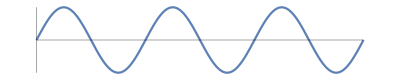

```mathematica
FullGraphics[Show[gr3]]
```